## Fitting a function

Here is an example of dropping an object from a tall cliff and recording its height after 1, 2, 3, 4, 5, and 6 seconds.  The estimated uncertainty for each measurement is 0.4 m.  Note that the weights input into the fit are equal to 1/uncertainty^2. The data points are then fit to a three parameter fit, using y = y_0 + v_0t – 1/2 g t^2.  The three free parameters are y_0 (initial height), v_0 (initial velocity), and g (acceleration due to gravity).

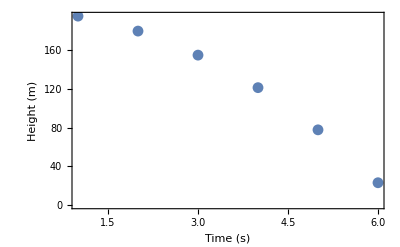

```mathematica
dispvstime = List[{1.0,195.6},{2.0,180.1},{3.0,155.2},{4.0,121.5},{5.0,77.8},{6.0,23.0}];
dispunc=List[0.4,0.4,0.4,0.4,0.4,0.4];
weights=1/dispunc^2;
datapoints = ListPlot[dispvstime,PlotRange->All,Frame->True,FrameLabel->{"Time (s)","Height (m)"}]
```

```mathematica
fitdata =NonlinearModelFit[dispvstime,y0+v0*t-0.5*g*t^2,{y0,v0,g},t,Weights->weights]
fitplot = Plot[fitdata[t],{t,0.0,6.5},PlotRange->All,PlotStyle->{Thickness[0.005], Red},Frame->True,FrameLabel->{"Time (s)","Height (m)"}];
fitdata["BestFitParameters"]
fitdata["ParameterErrors"]
fitdata["ParameterTable"]
```

FittedModel[200.61-0.426071 t-4.85179 t^2]

{y0→200.61,v0→-0.426071,g→9.70357}

{0.996489,0.65193,0.182339}

| Estimate | Standard Error | t-Statistic | P-Value
y0 | 200.61 | 0.996489 | 201.317 | 2.70266×10^-7
v0 | -0.426071 | 0.65193 | -0.653554 | 0.560024
g | 9.70357 | 0.182339 | 53.2173 | 0.0000146137

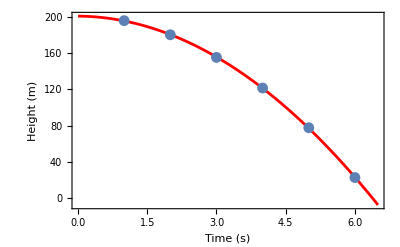

```mathematica
Show[fitplot,datapoints]
```

The fitted values for y0, v0, and g are 200.6 ± 1.0 m, 0.4 ± 0.7 m/s, and 9.70 ± 0.18 m/s^2.